```mathematica
$HistoryLength=0;ClearAll["Global`*"]; 
SetDirectory["/home/dan/ResearchLocal/adiabatic"];
```

```mathematica
fontweight="Bold"; fontsize=12;
```

## Weak Scaling (constant grids per core)

```mathematica
intelWS={
(*runID,cores,zones,cycles,walltime*)
{100,1*1*1,1*32^3,1000,216.9},
{101,2*2*2,8*32^3,1000,229.4},
{102,4*2*2,16*32^3,1000,232.6},
{103,4*3*2,24*32^3,1000,251.6},
{104,4*4*2,32*32^3,1000,250.0},
{105,4*4*3,48*32^3,1000,257.9},
{106,4*4*4,64*32^3,1000,256.1},
{107,6*6*6,216*32^3,1000,291.9},
{108,8*8*8,512*32^3,1000,327.3},
{109,10*10*10,1000*32^3,1000,358.4},
{100,1*1*1,1*32^3,1000,217.6},
{101,2*2*2,8*32^3,1000,236.4},
{102,4*2*2,16*32^3,1000,244.3},
{103,4*3*2,24*32^3,1000,257.4},
{104,4*4*2,32*32^3,1000,252.6},
{105,4*4*3,48*32^3,1000,260.8},
{106,4*4*4,64*32^3,1000,260.1},
{107,6*6*6,216*32^3,1000,287.5},
{108,8*8*8,512*32^3,1000,315.2},
{109,10*10*10,1000*32^3,1000,361.55},
{100,1*1*1,1*32^3,1000,217.4},
{101,2*2*2,8*32^3,1000,234.1},
{102,4*2*2,16*32^3,1000,242.8},
{103,4*3*2,24*32^3,1000,253.4},
{104,4*4*2,32*32^3,1000,250.4},
{105,4*4*3,48*32^3,1000,261.9},
{106,4*4*4,64*32^3,1000,260.8},
{107,6*6*6,216*32^3,1000,289.8},
{108,8*8*8,512*32^3,1000,317.8},
{109,10*10*10,1000*32^3,1000,354.7},
{110,12*12*12,1000*32^3,1000,423.1},
{110,14*14*14,1000*32^3,1000,498.6}
};
```

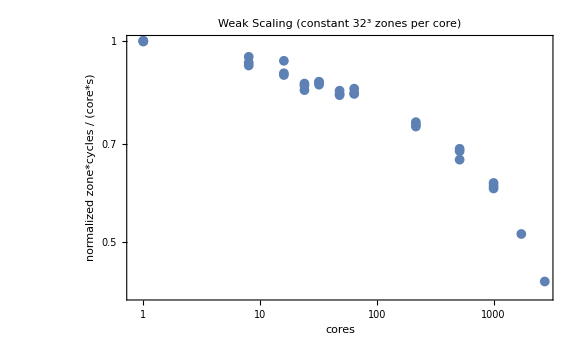

```mathematica
wsPlot=ListLogLogPlot[Transpose[{
intelWS[[All,2]],
(1/intelWS[[All,5]])/Mean[{(1/intelWS[[1,5]]),(1/intelWS[[11,5]]),(1/intelWS[[21,5]])}]
}]
,PlotLabel->"Weak Scaling (constant 32^3 zones per core)",FrameLabel->{"cores","normalized zone*cycles / (core*s)"},GridLines->{Table[24*i,{i,1,2}],{}},Frame->True,BaseStyle->{FontWeight->fontweight,FontSize->fontsize},PlotMarkers->{Automatic,10},ImageSize->Large]
```

```mathematica
Export["wsPlot2.png",wsPlot]
```

wsPlot2.png

## Strong Scaling (constant total number of grids)

```mathematica
256/16//N
```

16.

```mathematica
intelSS={
(*runID,cores,zones,cycles,walltime*)
{201,2^3,8^3*32^3,10,118.2},
{202,4^3,8^3*32^3,100,177.0},
{203,8^3,8^3*32^3,500,141.6},
{204,10^3,8^3*32^3,2000,}
};
```

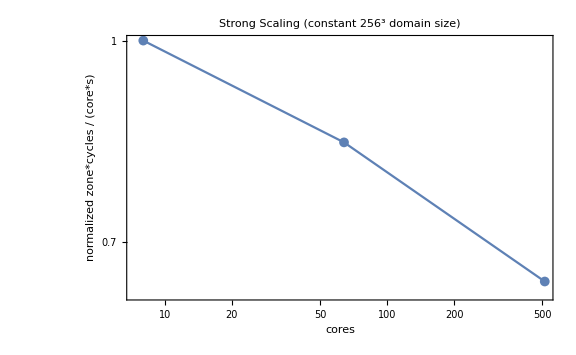

```mathematica
ssPlot=ListLogLogPlot[Transpose[{
intelSS[[All,2]],
(intelSS[[All,4]]/intelSS[[All,5]]/intelSS[[All,2]])/(intelSS[[1,4]]/intelSS[[1,5]]/intelSS[[1,2]])
}]
,PlotLabel->"Strong Scaling (constant 256^3 domain size)",FrameLabel->{"cores","normalized zone*cycles / (core*s)"},Frame->True,BaseStyle->{FontWeight->fontweight,FontSize->fontsize},PlotMarkers->{Automatic,10},ImageSize->Large,Joined->True]
```

```mathematica
Export["ssPlot2.png",wsPlot]
```

ssPlot2.png

## Switch testing

```mathematica
oneSwitch={112740,108649,98819,106535};
nSwitch={100615,114145,111654,100102};
Mean[oneSwitch]//N
Mean[nSwitch]//N
```

106686.

106629.

```mathematica
oneSwitch={102883,101935,106899,105711,102565};
nSwitch={105121,99320,107438,104496,103072};
Mean[oneSwitch]//N
Mean[nSwitch]//N
```

103999.

103889.

## Constant number of cores scaling

```mathematica
data={
(*runID,cores,zones,cycles,zcpws*)
{400,8^3,8^3*8^3,1000,33440},
{401,8^3,8^3*16^3,1000,75609},
{402,8^3,8^3*32^3,1000,104019},
{403,8^3,8^3*64^3,100,139228},
{404,8^3,8^3*128^3,10,155655}
};
```

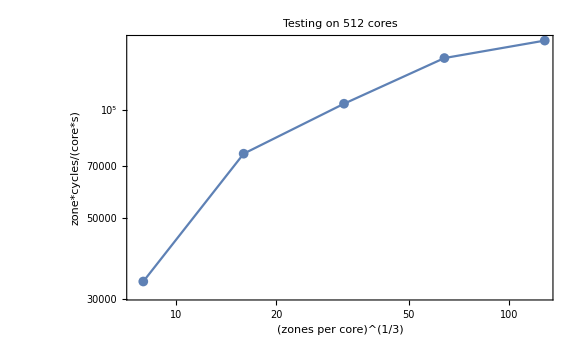

```mathematica
dataPlot=ListLogLogPlot[Transpose[{(data[[All,3]]/data[[All,2]])^(1/3),data[[All,5]]}]
,PlotLabel->"Testing on 512 cores",FrameLabel->{"(zones per core)^(1/3)","zone*cycles/(core*s)"}, Frame->True,BaseStyle->{FontWeight->fontweight,FontSize->fontsize},PlotMarkers->{Automatic,10},ImageSize->Large,Joined->True]
```

```mathematica
Export["ssPlot3.png",dataPlot]
```

ssPlot3.png

## Weak Scaling (@64 grids per core)

```mathematica
data={
(*runID,cores,zones,cycles,zcpws*)
{400,1^3,1^3*64^3,100,164264},
{401,2^3,2^3*64^3,100,156819},
{402,4^3,4^3*64^3,100,147968},
{403,8^3,8^3*64^3,100,139086},
{404,10^3,10^3*64^3,100,130516},
{405,12^3,8^3*64^3,100,128344},
{406,14^3,8^3*64^3,100,122169}
};
```

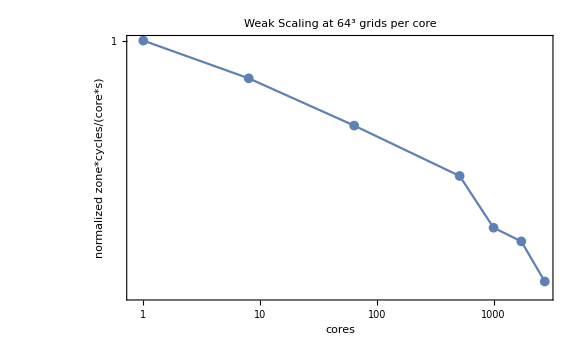

```mathematica
dataPlot=ListLogLogPlot[Transpose[{data[[All,2]],data[[All,5]]/data[[1,5]]}]
,PlotLabel->"Weak Scaling at 64^3 grids per core",FrameLabel->{"cores","normalized zone*cycles/(core*s)"}, Frame->True,BaseStyle->{FontWeight->fontweight,FontSize->fontsize},PlotMarkers->{Automatic,10},ImageSize->Large,Joined->True]
```

```mathematica
Export["ws64Plot.png",dataPlot]
```

ws64Plot.png